3

2048

2048

2048

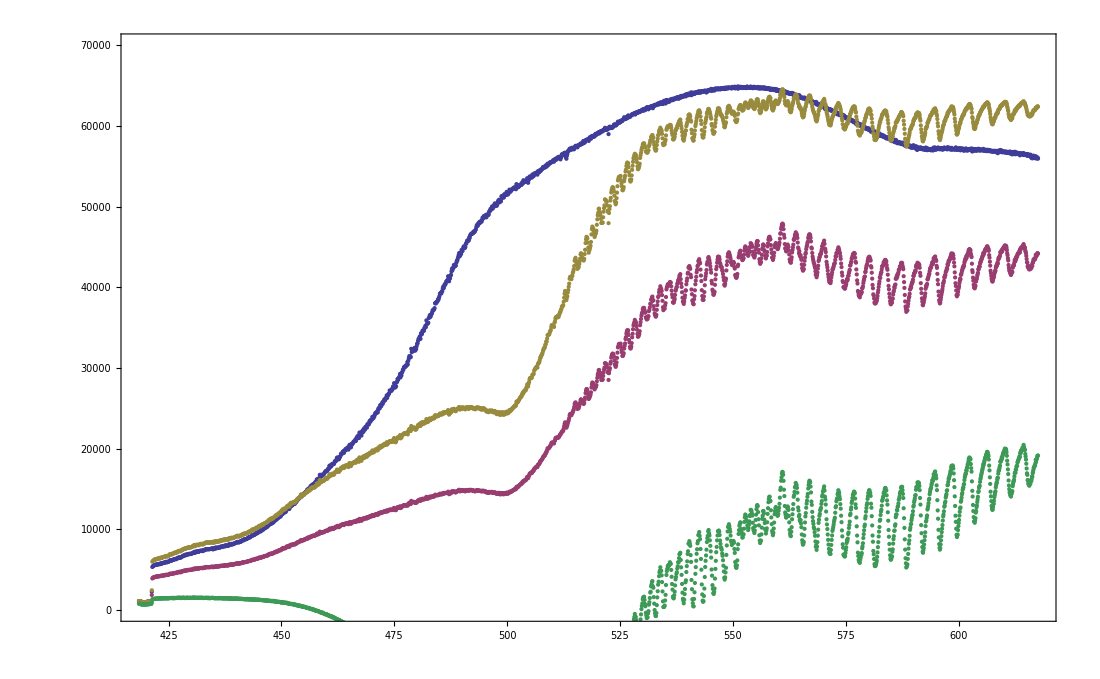

```mathematica
names={"03_Halogen_ngg10.txt","04_I2_ngg10_10ms.txt","04_I2_ngg10_17ms.txt"};
imp=Table[Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>names[[i]],"Table",NumberPoint->","],{i,1,Length[names]}];
data=Table[Drop[imp[[i]],17],{i,1,3}];
data=Table[Drop[data[[i]],-1],{i,1,3}];
Length[data]
Length[data[[1]]]
Length[data[[2]]]
Length[data[[3]]]
datab=data;
datab[[2,All,2]]=1.7*data[[2,All,2]];
datab[[3,All,2]]=datab[[3,All,2]]-data[[1,All,2]];
datab[[2,All,2]]=datab[[2,All,2]]-data[[1,All,2]];
ListPlot[{data[[1]],data[[2]],data[[3]],datab[[2]]},PlotRange->{0,70000},ImageSize->1100,Frame->True]
```

```mathematica
'
```

47

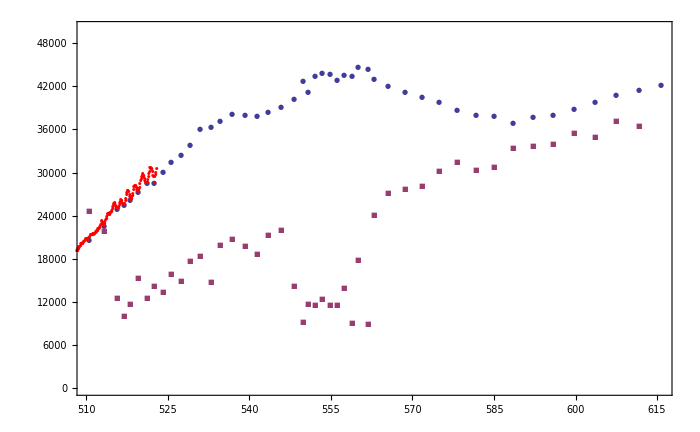

{{510.38,20648.4},{513.12,22594.8},{515.55,24918.6},{516.95,25534.3},{518.06,26152.2},{519.36,27342.},{521.06,28510.6},{522.45,28514.1},{524.03,30137.6},{525.52,31489.5},{527.29,32406.1},{528.95,33866.4},{530.91,36006.5},{532.95,36370.8},{534.59,37163.},{536.81,38085.2},{539.11,37937.6},{541.3,37900.8},{543.38,38435.5},{545.74,39060.8},{548.18,40202.9},{549.76,42767.4},{550.78,41168.5},{552.08,43372.7},{553.37,43897.2},{554.75,43685.8},{556.03,42904.3},{557.31,43573.6},{558.86,43389.9},{559.86,44733.5},{561.84,44442.5},{562.83,43045.1},{565.51,42056.3},{568.53,41244.5},{571.61,40516.4},{574.74,39839.5},{578.1,38753.1},{581.6,38001.},{584.97,37887.3},{588.39,36955.},{592.1,37770.3},{595.84,37995.2},{599.61,38881.9},{603.56,39868.5},{607.45,40721.4},{611.58,41522.3},{615.64,42203.3}}

```mathematica
l=Drop[data[[2]],750];
minima={};
Δ=4;
For[i=Δ+1,i≤Length[l]-(Δ+1),i++,
If[FreeQ[
Table[l[[i+n,2]]≥ l[[i,2]],{n,-Δ,Δ}],
False],
minima=Append[minima,l[[i]]]
]
];
Length[minima]
Show[
ListPlot[{minima,x1b},PlotRange->{0,50000},ImageSize->700,Frame->True,PlotMarkers->{Automatic,7}],
ListPlot[l,PlotMarkers->{Automatic,2},PlotStyle->Red]
]
minima
```

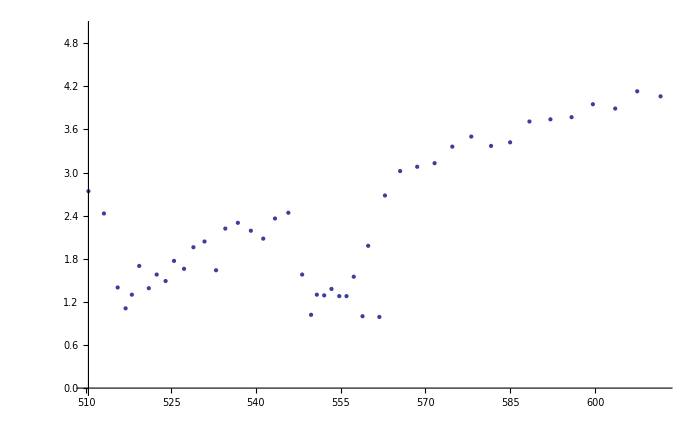

{{510.38,104.626},{513.12,91.8579},{515.55,52.5302},{516.95,41.4471},{518.06,48.3164},{519.36,62.8192},{521.06,51.0602},{522.45,57.7107},{524.03,54.1054},{525.52,63.8755},{527.29,59.5174},{528.95,69.7944},{530.91,72.0979},{532.95,57.5621},{534.59,77.3591},{536.81,79.4749},{539.11,75.0462},{541.3,70.7166},{543.38,79.5834},{545.74,81.5607},{548.18,52.4277},{549.76,33.686},{550.78,42.7527},{552.08,42.2252},{553.37,44.9538},{554.75,41.4968},{556.03,41.3062},{557.31,49.7659},{558.86,31.9608},{559.86,62.9467},{561.84,31.3073},{562.83,84.201},{565.51,93.9319},{568.53,94.7758},{571.61,95.2737},{574.74,101.126},{578.1,104.098},{581.6,99.054},{584.97,99.3636},{588.39,106.491},{592.1,106.01},{595.84,105.522},{599.61,109.146},{603.56,106.101},{607.45,111.17},{611.58,107.832}}

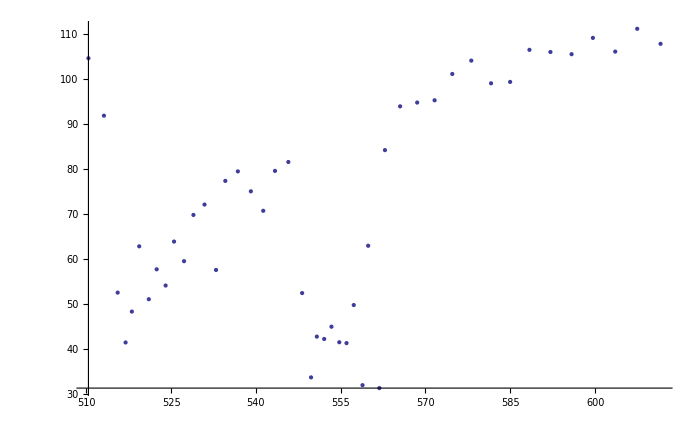

```mathematica
x1=Table[{minima[[i,1]],minima[[i+1,1]]-minima[[i,1]]},{i,1,Length[minima]-1}];
x1b=x1;
x1b[[All,2]]=9000*x1b[[All,2]];
ListPlot[x1,ImageSize->700,PlotRange->{0,5}]
x2=Table[{minima[[i,1]],1/(minima[[i,1]]*10^-7)-1/(minima[[i+1,1]]*10^-7)},{i,1,Length[minima]-1}]
ListPlot[x2,ImageSize->700,PlotRange->Automatic]
```